Load CRNT

reactions and transitions: (0→s | μ_0 s_0
i1+s→2 i1 | (i_1 μ_1 R_1 s)/s_0
i2+s→2 i2 | (i_2 μ_2 R_2 s)/s_0
i12+s→2 i12 | (i_12 μ_3 R_3 s)/s_0
i1+i2→i12+i2 | γ_1 i_1 i_2
i1+i2→i1+i12 | γ_2 i_1 i_2
i1+i12→2 i12 | η_1 i_1 i_12
i12+i2→2 i12 | η_2 i_12 i_2
i12+s→i1+i12 | β_1 i_12 s
i12+s→i12+i2 | β_2 i_12 s
s→0 | μ_0 s
i1→0 | i_1 μ_1
i2→0 | i_2 μ_2
i12→0 | i_12 μ_3)

Minimal siphons: {T_1={i_1,i_12},T_2={i_2,i_12}}

IGMS edges: {1→2,2→1}

Cycles in IGMS (1 found):

Cycle 1: {1->2,2->1}

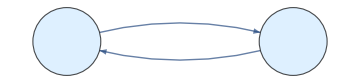

siphons are{{i_1,i_12},{i_2,i_12}} edges are{1→2,2→1}  DFE is{s→s_0,i_1→0,i_12→0,i_2→0} repr. functions  {(R_1 s)/s_0,(R_2 s)/s_0,(R_3 s)/s_0}

K=((R_1 s)/s_0 | (β_1 s)/μ_3 | 0
0 | (R_3 s)/s_0 | 0
0 | (β_2 s)/μ_3 | (R_2 s)/s_0)F=((μ_1 R_1 s)/s_0 | β_1 s | 0
0 | (μ_3 R_3 s)/s_0 | 0
0 | β_2 s | (μ_2 R_2 s)/s_0)V=(μ_1 | 0 | 0
0 | μ_3 | 0
0 | 0 | μ_2)

Ko.pdf

((R_1 s)/s_0 | 0 | (β_1 s)/μ_3
0 | (R_2 s)/s_0 | (β_2 s)/μ_3
0 | 0 | (R_3 s)/s_0)

((μ_1 R_1 s)/s_0 | 0 | β_1 s
0 | (μ_2 R_2 s)/s_0 | β_2 s
0 | 0 | (μ_3 R_3 s)/s_0)

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];Format[mu0]:=Subscript[μ,0];
Format[R1]:=Subscript[R,1];Format[R2]:=Subscript[R,2];Format[R3]:=Subscript[R,3];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];Format[s0]:=Subscript[s,0];
Format[th]:=θ;
Format[La]:=Λ;
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];

cLog={be1->0,be2->0,ga1->0,ga2->0,b->r*s*(1-s/s0),mu0->0};
cbg={be1->0,be2->0,ga1->0,ga2->0};
cbe={be1->0,be2->0};cb=b->s0 mu0;cga={ga1->0,ga2->0};
cet={et1->s13 mu1 mu3 (R1-R3)/((s0-s13)mu0 s0),
et2->s23 mu2 mu3 (R2-R3)/((s0-s23)mu0 s0)};

c3={i12->0};c2={i2->0};c1={i1->0};cb=b->r*s*(1-s/s0);
(*Two-Strain Coinfection Model with Logistic Growth*)
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};
rts={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,ga1*i1*i2,ga2*i1*i2,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];

Export["Ko.pdf",graph]
per={1,3,2};K[[per,per]]//MatrixForm
F[[per,per]]//MatrixForm
```

Minimal siphons: {T_1={i_12}}

IGMS edges: {}

IGMS is acyclic (no cycles found)

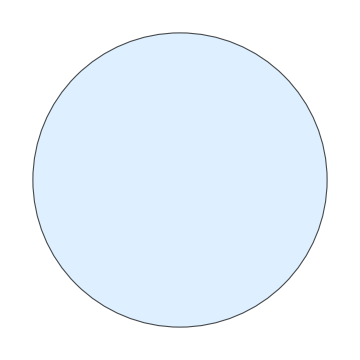

siphons are{{i_12}} edges are{}  DFE is{i_1→0,i_2→0,s→s_0,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,s→s_0/R_1,i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_12→0} repr. functions  {(μ_3 R_3 s+η_1 i_1 s_0+η_2 i_2 s_0)/(μ_3 s_0)}

K=((η_1 i_1+η_2 i_2+(μ_3 R_3 s)/s_0)/μ_3)F=(η_1 i_1+η_2 i_2+(μ_3 R_3 s)/s_0)V=(μ_3)

Ko.pdf

```mathematica
RNb={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};

rtsb={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RNb,rtsb];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];

Export["Ko.pdf",graph]
per={1,3,2};K[[per,per]]//MatrixForm
F[[per,per]]//MatrixForm
```

reactions and transitions: (0→s | μ_0 s_0
i1+s→2 i1 | (i_1 μ_1 R_1 s)/s_0
i2+s→2 i2 | (i_2 μ_2 R_2 s)/s_0
i12+s→2 i12 | (i_12 μ_3 R_3 s)/s_0
i1+i12→2 i12 | η_1 i_1 i_12
i12+i2→2 i12 | η_2 i_12 i_2
s→0 | μ_0 s
i1→0 | i_1 μ_1
i2→0 | i_2 μ_2
i12→0 | i_12 μ_3)

RHS=(k1-(i_1 k2+i_2 k3+i_12 k4+k7) s
-i_1 (i_12 k5+k8-k2 s)
-i_2 (i_12 k6+k9-k3 s)
i_12 (-k10+i_1 k5+i_2 k6+k4 s))mSi={{i_1},{i_2},{i_12}}

Minimal siphons: {T_1={i_1},T_2={i_2},T_3={i_12}}

IGMS edges: {1→3,2→3,3→1,3→2}

Cycles in IGMS (2 found):

Cycle 1: {2->3,3->2}

Cycle 2: {1->3,3->1}

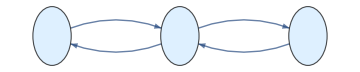

siphons are{{i_1},{i_2},{i_12}} edges are{1→3,2→3,3→1,3→2}  DFE is{s→s_0,i_1→0,i_12→0,i_2→0} repr. functions  {(R_1 s)/s_0,(R_2 s)/s_0,(R_3 s)/s_0}

K=((R_1 s)/s_0 | 0 | 0
0 | (R_3 s)/s_0 | 0
0 | 0 | (R_2 s)/s_0)F=((μ_1 R_1 s)/s_0 | 0 | 0
0 | (μ_3 R_3 s)/s_0 | 0
0 | 0 | (μ_2 R_2 s)/s_0)V=(μ_1 | 0 | 0
0 | μ_3 | 0
0 | 0 | μ_2)

Kbd.pdf

```mathematica
(*part. case*)RNbg={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};

rtsbg={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,et1*i1*i12,et2*i2*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print["reactions and transitions: ",Transpose[{RNbg,rtsbg}]//MatrixForm]
{spe, al, be, gamma, Rv, RHS,mSi, {defFormula, defTerms, defResult}}=extMat[RNbg];
Print["RHS=",RHS//FullSimplify//MatrixForm,"mSi=",mSi];
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RNbg,rtsbg];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
Export["Kbd.pdf",graph]
```

```mathematica
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,gam,Et}=bdCo[RNbg, rtsbg];
Print["The ", Et//Length ," Et elts have  3,3,2 coms "];
Print["Et1= ",Et1=Et[[1]],"Et2= ",
Et2=Et[[2]],"Et3= ",
Et3=Et[[3]]];
eq=Thread[(RHS/.cbg/.c2)==0];
so=Solve[eq,var]//FullSimplify;(*4 solutions*)
Print["the",so//Length,"sols on siphon 2 are",so];
jac=Grad[RHS,var];
```

The 3 Et elts have  3,3,2 coms

Et1= {{i_12→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_1→0},{i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3),i_2→0,s→s_0/R_3,i_1→0},{i_12→-(μ_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0-η_2 μ_0 R_2 s_0))/(η_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0)),i_2→(μ_2 μ_3^2 R_2-μ_2 μ_3^2 R_3+η_2 μ_0 μ_3 s_0-η_2 μ_0 μ_3 R_3 s_0)/(η_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0)),s→(η_2 μ_0 s_0^2)/(μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0),i_1→0}}Et2= {{i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0,s→s_0/R_1,i_2→0},{i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3),s→s_0/R_3,i_2→0},{i_1→(μ_1 μ_3^2 R_1-μ_1 μ_3^2 R_3+η_1 μ_0 μ_3 s_0-η_1 μ_0 μ_3 R_3 s_0)/(η_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0)),i_12→-(μ_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0-η_1 μ_0 R_1 s_0))/(η_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0)),s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0),i_2→0}}Et3= {{i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,s→s_0/R_1,i_12→0},{i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_12→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

the4sols on siphon 2 are{{s→s_0,i_1→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0},{s→s_0/R_3,i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))}}

```mathematica
(*all fps*)
eq=Thread[RHS==0];so=Solve[eq,var];(*7 solutions*)
Print[so//Length," sols"]
so//FullSimplify
cD=so[[1]];cE1=so[[2]];cE2=so[[3]];cE3=so[[4]];cEE=so[[6]];c13=so[[5]];
Print["s13= ",s13=s/.c13//FullSimplify]
i131=i1/.c13; i131-mu3(1-R3 s13/s0) /et1//FullSimplify
i133=i12/.c13//FullSimplify;
i133-(R1 s13/s0 -1)mu1/et1//FullSimplify
c23=so[[7]];
con=Join[cp,Thread[Drop[var/.cE1,{3,4}]>0]];
Print["E1 exists if"]
re1=reCL[Reduce[con]//Factor]
(*con=Join[cp,Thread[Drop[var/.c13,3]>0]];
Print["E13 exists if"]
re11=reCL[Reduce[con]//Factor]*)
```

7 sols

{{s→s_0,i_1→0,i_2→0,i_3→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,i_3→0},{s→s_0/R_2,i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),i_3→0},{s→s_0/R_3,i_1→0,i_2→0,i_3→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(μ_0 s_0^2 η_1)/(μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1),i_1→μ_3 (1/η_1-(μ_0 R_3 s_0)/(μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)),i_2→0,i_3→μ_1 (-1/η_1+(μ_0 R_1 s_0)/(μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1))},{s→(s_0 (μ_2 η_1-μ_1 η_2))/(μ_2 R_2 η_1-μ_1 R_1 η_2),i_1→(μ_2^2 μ_3 (R_2-R_3) η_1+μ_2 (μ_1 μ_3 (-R_2+R_3)-μ_0 (-1+R_2) s_0 η_1) η_2+μ_0 μ_1 (-1+R_1) s_0 η_2^2)/((μ_2 η_1-μ_1 η_2) (μ_2 R_2 η_1-μ_1 R_1 η_2)),i_2→(μ_0 s_0 η_1)/(μ_2 η_1-μ_1 η_2)+(μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)/(-μ_2 R_2 η_1+μ_1 R_1 η_2),i_3→(μ_1 μ_2 (-R_1+R_2))/(-μ_2 R_2 η_1+μ_1 R_1 η_2)},{s→(μ_0 s_0^2 η_2)/(μ_2 μ_3 (R_2-R_3)+μ_0 s_0 η_2),i_1→0,i_2→μ_3 (1/η_2-(μ_0 R_3 s_0)/(μ_2 μ_3 (R_2-R_3)+μ_0 s_0 η_2)),i_3→μ_2 (-1/η_2+(μ_0 R_2 s_0)/(μ_2 μ_3 (R_2-R_3)+μ_0 s_0 η_2))}}

s13= (μ_0 s_0^2 η_1)/(μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)

0

0

E1 exists if

R_1>1

```mathematica
(*Stab E1*)
j1=jac/.cE1//FullSimplify;j1//MatrixForm
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
```

```mathematica
lSta
qSta
Print["E1 stable if R1(s13) >1"]
re=reCL[Reduce[Join[cp,lSta,qSta]]//FullSimplify]//FullSimplify
cpL=And@@Drop[cp,-1]&&R1>1;
re1=FullSimplify[re,cpL]
```

{μ_2 R_1-μ_2 R_2>0,μ_1 μ_3 R_1-μ_1 μ_3 R_3+μ_0 s_0 η_1-μ_0 R_1 s_0 η_1>0}

{μ_0 R_1>0,-μ_0 μ_1+μ_0 μ_1 R_1>0}

E1 stable if R1(s13) >1

(R_1>R_3&&R_3>1&&μ_0<(μ_1 μ_3 (R_1-R_3))/((-1+R_1) s_0 η_1)&&R_2<R_1)||(R_1>1&&R_1>R_2&&μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_3≤1)

μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_1>R_2&&(R_1>R_3||R_3≤1)

```mathematica
(*Stab E3*)j3=jac/.cE3//FullSimplify;j3//MatrixForm
Print[" At cE3, chp of jac, ch3, factorizes as"]
ch3=Numerator[Together[CharacteristicPolynomial[j3,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch3,par];
ll//Length
ql//Length
hDeg

ret=Reduce[Join[cp,lSta,qSta,{R3>1(*,R1>R2*)}]]//FullSimplify;
cond=And@@cp&&R3>1
Print["E3 stable if R1(s11) <1"]
re3=FullSimplify[ret,cond]
re3//Length
re31=re3[[1]]
re31//Length
re32=re3[[2]];re=BooleanMinimize[LogicalExpand[re3]]//FullSimplify
FullSimplify[re3,cond]
FullSimplify[re,cond]
lo=LogicalExpand[re]
Resolve[lo,Reals]
```

(-μ_0 R_3 | -(μ_1 R_1)/R_3 | -(μ_2 R_2)/R_3 | -μ_3
0 | (μ_1 μ_3 (R_1-R_3)-μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | 0 | 0
0 | 0 | (μ_2 μ_3 (R_2-R_3)-μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0
μ_0 (-1+R_3) | (μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | (μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0)

At cE3, chp of jac, ch3, factorizes as

(-μ_0 μ_3+μ_0 μ_3 R_3+μ_0 R_3 u+u^2) (-μ_1 μ_3 R_1+μ_1 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_1+μ_0 R_3 s_0 η_1) (-μ_2 μ_3 R_2+μ_2 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_2+μ_0 R_3 s_0 η_2)

2

1

{}

μ_0>0&&μ_1>0&&μ_2>0&&μ_3>0&&R_1>0&&R_2>0&&R_3>0&&s_0>0&&η_1>0&&η_2>0&&R_3>1

E3 stable if R1(s11) <1

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

2

R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0

2

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

```mathematica
(*Stab E1*)
j13=jac/.c13//FullSimplify;
Print[" At cE13, chp of jac factorizes as"]
ch13=Numerator[Together[CharacteristicPolynomial[j13,u]]]//Factor
ch13//Length
co2=CoefficientList[ch13[[2]],u]//FullSimplify
```

At cE13, chp of jac factorizes as

(μ_1^4 μ_3^4 R_1^3-3 μ_1^4 μ_3^4 R_1^2 R_3+3 μ_1^4 μ_3^4 R_1 R_3^2-μ_1^4 μ_3^4 R_3^3-μ_1^3 μ_3^3 R_1^3 u^2+3 μ_1^3 μ_3^3 R_1^2 R_3 u^2-3 μ_1^3 μ_3^3 R_1 R_3^2 u^2+μ_1^3 μ_3^3 R_3^3 u^2+3 μ_0 μ_1^3 μ_3^3 R_1^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_1^3 s_0 η_1-6 μ_0 μ_1^3 μ_3^3 R_1 R_3 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1^2 R_3 s_0 η_1+3 μ_0 μ_1^3 μ_3^3 R_3^2 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1 R_3^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_3^3 s_0 η_1+μ_1^3 μ_3^3 R_1^2 s_0 u η_1-μ_0 μ_1^3 μ_3^2 R_1^3 s_0 u η_1-2 μ_1^3 μ_3^3 R_1 R_3 s_0 u η_1+μ_0 μ_1^3 μ_3^2 R_1^2 R_3 s_0 u η_1+μ_1^3 μ_3^3 R_3^2 s_0 u η_1+μ_0 μ_1^2 μ_3^3 R_1 R_3^2 s_0 u η_1-μ_0 μ_1^2 μ_3^3 R_3^3 s_0 u η_1-3 μ_0 μ_1^2 μ_3^2 R_1^2 s_0 u^2 η_1+6 μ_0 μ_1^2 μ_3^2 R_1 R_3 s_0 u^2 η_1-3 μ_0 μ_1^2 μ_3^2 R_3^2 s_0 u^2 η_1-μ_1^2 μ_3^2 R_1^2 s_0 u^3 η_1+2 μ_1^2 μ_3^2 R_1 R_3 s_0 u^3 η_1-μ_1^2 μ_3^2 R_3^2 s_0 u^3 η_1+3 μ_0^2 μ_1^2 μ_3^2 R_1 s_0^2 η_1^2-2 μ_0^2 μ_1^2 μ_3^2 R_1^2 s_0^2 η_1^2-3 μ_0^2 μ_1^2 μ_3^2 R_3 s_0^2 η_1^2+μ_0^2 μ_1^2 μ_3^2 R_1^2 R_3 s_0^2 η_1^2+2 μ_0^2 μ_1^2 μ_3^2 R_3^2 s_0^2 η_1^2-μ_0^2 μ_1^2 μ_3^2 R_1 R_3^2 s_0^2 η_1^2+2 μ_0 μ_1^2 μ_3^2 R_1 s_0^2 u η_1^2-μ_0^2 μ_1^2 μ_3 R_1^2 s_0^2 u η_1^2-μ_0 μ_1^2 μ_3^2 R_1^2 s_0^2 u η_1^2-2 μ_0 μ_1^2 μ_3^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1^2 μ_3 R_1^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1 μ_3^2 R_3^2 s_0^2 u η_1^2+μ_0 μ_1^2 μ_3^2 R_3^2 s_0^2 u η_1^2-μ_0^2 μ_1 μ_3^2 R_1 R_3^2 s_0^2 u η_1^2-3 μ_0^2 μ_1 μ_3 R_1 s_0^2 u^2 η_1^2+3 μ_0^2 μ_1 μ_3 R_3 s_0^2 u^2 η_1^2-2 μ_0 μ_1 μ_3 R_1 s_0^2 u^3 η_1^2+2 μ_0 μ_1 μ_3 R_3 s_0^2 u^3 η_1^2+μ_0^3 μ_1 μ_3 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_1 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_3 s_0^3 η_1^3+μ_0^3 μ_1 μ_3 R_1 R_3 s_0^3 η_1^3+μ_0^2 μ_1 μ_3 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_1 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_3 s_0^3 u η_1^3+μ_0^2 μ_1 μ_3 R_1 R_3 s_0^3 u η_1^3-μ_0^3 s_0^3 u^2 η_1^3-μ_0^2 s_0^3 u^3 η_1^3) (-μ_1 μ_2 μ_3 R_1 η_1+μ_1 μ_2 μ_3 R_3 η_1-μ_1 μ_3 R_1 u η_1+μ_1 μ_3 R_3 u η_1-μ_0 μ_2 s_0 η_1^2+μ_0 μ_2 R_2 s_0 η_1^2-μ_0 s_0 u η_1^2+μ_1^2 μ_3 R_1 η_2-μ_1^2 μ_3 R_3 η_2+μ_0 μ_1 s_0 η_1 η_2-μ_0 μ_1 R_1 s_0 η_1 η_2)

2

{μ_0 μ_2 (-1+R_2) s_0 η_1^2+μ_1^2 μ_3 (R_1-R_3) η_2+μ_1 η_1 (μ_2 μ_3 (-R_1+R_3)-μ_0 (-1+R_1) s_0 η_2),-η_1 (μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)}

```mathematica
v23=Drop[var/.c23//FullSimplify,{2}];
(*Print["E23 exists if"]*)
re2=reCL[Factor/@Reduce[Join[cp,Thread[v23>0]]]];
Print["EE exists if"]
reE=reCL[Factor/@Reduce[Join[cp,Thread[(var/.cEE)>0],{R1>R2}]]]
reE[[2,1]]
```

EE exists if

R_2>1&&R_1>R_2&&0<μ_1<(μ_2 (-1+R_2) η_1)/((-1+R_1) η_2)&&0<R_3<(μ_2 R_2 η_1-μ_1 R_1 η_2)/(μ_2 η_1-μ_1 η_2)&&(μ_1 μ_3 (R_1-R_3) (-μ_2 η_1+μ_1 η_2))/(s_0 η_1 (μ_2 η_1-μ_2 R_2 η_1-μ_1 η_2+μ_1 R_1 η_2))<μ_0<(μ_2 μ_3 (R_2-R_3) (μ_2 η_1-μ_1 η_2))/(s_0 η_2 (-μ_2 η_1+μ_2 R_2 η_1+μ_1 η_2-μ_1 R_1 η_2))

```mathematica
cpl=And@@cp;
fi=FindInstance[reE&&re1&&re2&&cpl&&R1>1&&R2>1&&R3>1,par]
```

{{μ_0→5/4,μ_1→3/2,μ_2→1,μ_3→1,R_1→39/32,R_2→5/4,R_3→17/16,s_0→1,η_1→1,η_2→1}}

```mathematica
Timing[re=reCL[Reduce[reE&&re1&&re2&&cpl&&R1>1&&R2>1&&R3>1]//FullSimplify]]
```

$Aborted

```mathematica
jEE=jac/.cEE//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[jEE,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
ll//Length
ql//Length
hDeg
```

At cE1, chp of jac, ch1, factorizes as

0

0

```mathematica
j11=jac/.c11//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j11,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
ll//Length
ql//Length
hDeg
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

At cE1, chp of jac, ch1, factorizes as

0

0

b>0&&μ_1>0&&μ_2>0&&α_1>0&&α_2>0&&α_3>0&&β_1>0&&β_2>0&&γ_1>0&&γ_2>0&&η_1>0&&η_2>0&&μ_0>0&&μ_3>0

```mathematica
jD=jac/.cD//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[jD,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
ll//Length
ql//Length
hDeg
re1=reCL[Reduce[Join[cp,lSta,qSta]]//FullSimplify]
```

At cE1, chp of jac, ch1, factorizes as

-((u+μ_0) (b α_1-μ_1 μ_0-u μ_0) (b α_2-μ_2 μ_0-u μ_0) (b α_3-u μ_0-μ_0 μ_3))

4

0

{}

b α_3<μ_0 μ_3&&b α_2<μ_2 μ_0&&b α_1<μ_1 μ_0

```mathematica
coPb = FindInstance[
      Join[cp, {(R12/.cbg) > 1, (R21/.cbg) > 1}, 
       Table[1 < (R0A[[k]]/.cbg) /. E0, {k, R0A//Length}]], par]//Flatten

eqP=Thread[(RHS/.cbg/.coPb)==0];soN=Solve[eqP,var]//N;(*7 solutions*)
Print[so//Length," sols",soN]
(*Simple function to remove solutions with any negative values*)remNeg[sol_]:=Select[sol,AllTrue[Values[#],#>=0&]&];
soP=remNeg[soN]
soP//Length
```

{b→3,α_1→3/8,α_2→1/2,α_3→1,β_1→1,β_2→1,γ_1→1,γ_2→1,η_1→1,η_2→1,μ_0→1,μ_1→1,μ_2→1,μ_3→1}

7 sols{{s→1.,i_1→0.,i_2→0.,i_12→2.},{s→2.,i_1→0.,i_2→1.,i_12→0.},{s→2.66667,i_1→0.333333,i_2→0.,i_12→0.},{s→3.,i_1→0.,i_2→0.,i_12→0.},{s→6.,i_1→0.,i_2→-5.,i_12→2.},{s→8.,i_1→-7.,i_2→0.,i_12→2.}}

{{s→1.,i_1→0.,i_2→0.,i_12→2.},{s→2.,i_1→0.,i_2→1.,i_12→0.},{s→2.66667,i_1→0.333333,i_2→0.,i_12→0.},{s→3.,i_1→0.,i_2→0.,i_12→0.}}

4

```mathematica
(*Simple 3-line function to find positivity conditions for all fixed points*)allP[sol_]:=Block[{positivityConditions},positivityConditions=Flatten[Table[Thread[(var/. sol[[k]])>=0],{k,Length[sol]}]];
Reduce[Join[positivityConditions,cp]]];
allP[so]
```

7 sols

{{s→b/μ_0,i_1→0,i_2→0,i_12→0},{s→μ_1/α_1,i_1→-μ_0/α_1+b/μ_1,i_2→0,i_12→0},{s→μ_2/α_2,i_1→0,i_2→-μ_0/α_2+b/μ_2,i_12→0},{s→(η_2 μ_1-η_1 μ_2)/(-α_2 η_1+α_1 η_2),i_1→(b η_2 (-α_2 η_1+α_1 η_2)-(η_2 μ_1-η_1 μ_2) (η_2 μ_0-α_3 μ_2+α_2 μ_3))/((α_2 η_1-α_1 η_2) (-η_2 μ_1+η_1 μ_2)),i_2→(b η_1)/(-η_2 μ_1+η_1 μ_2)+(η_1 μ_0-α_3 μ_1+α_1 μ_3)/(-α_2 η_1+α_1 η_2),i_12→(α_2 μ_1-α_1 μ_2)/(-α_2 η_1+α_1 η_2)},{s→μ_3/α_3,i_1→0,i_2→0,i_12→-μ_0/α_3+b/μ_3},{s→(b η_1)/(η_1 μ_0-α_3 μ_1+α_1 μ_3),i_1→μ_3/η_1-(b α_3)/(η_1 μ_0-α_3 μ_1+α_1 μ_3),i_2→0,i_12→-μ_1/η_1+(b α_1)/(η_1 μ_0-α_3 μ_1+α_1 μ_3)},{s→(b η_2)/(η_2 μ_0-α_3 μ_2+α_2 μ_3),i_1→0,i_2→μ_3/η_2-(b α_3)/(η_2 μ_0-α_3 μ_2+α_2 μ_3),i_12→-μ_2/η_2+(b α_2)/(η_2 μ_0-α_3 μ_2+α_2 μ_3)}}

$Aborted

```mathematica
keepQ[sol_]:=Reduce[parAss&&And@@Thread[(var/. sol)>=0],par,Reals]=!=False;RHSO=RHS/.cLog;parO=Par[RHSO,var];
(*ct=Join[Thread[var>=0],Thread[parO>0]];*)
eqO=Join[eq/.cLog,Thread[parO>0]];so=Solve[(eq/.cLog),var];
(*assumptions and equations*)eq=Thread[RHS==0];
RHSO=RHS/. cLog;
parO=Par[RHSO,var];cpO=Thread[parO>0];
parAss=And@@cpO;
(*solve*)
so=Solve[eq/. cLog,var];(*10 solutions*)
      
so8=Select[so,keepQ];  
allZeroQ[sol_]:=And@@((#/. sol)===0&/@var);

so7=DeleteCases[so8,_?(allZeroQ)];   (*drop {s->0,i1->0,i2->0,i12->0}*)
so7v=remZ/@(var/.so7//Factor);wh=whenP/@so7v//FullSimplify;
Print[so7v//Length," sols ", so7]
Print[" with pos cnds"]
ClearAll[rmL];
SetAttributes[rmL,HoldFirst];

rmL[pat_]:=Function[{expr},Module[{p=HoldPattern[pat],parts},If[Head[expr]===And,parts=DeleteCases[List@@Unevaluated[expr],p];
Switch[Length@parts,0,True,1,First@parts,_,And@@parts],If[MatchQ[expr,p],True,expr]]],HoldAll];

(*examples*)
whS=rmL[mu0<r]/@wh
```

$Aborted

7 sols {{s→(s0 (r-μ_0))/r,i_1→0,i_2→0,i_12→0},{s→μ_3/α_3,i_1→0,i_2→0,i_12→-(-r s0 α_3+s0 α_3 μ_0+r μ_3)/(s0 α_3^2)},{s→-(-r s0 η_2+s0 η_2 μ_0-s0 α_3 μ_2+s0 α_2 μ_3)/(r η_2),i_1→0,i_2→-(r s0 α_3 η_2-s0 α_3 η_2 μ_0+s0 α_3^2 μ_2-s0 α_2 α_3 μ_3-r η_2 μ_3)/(r η_2^2),i_12→-(-r s0 α_2 η_2+s0 α_2 η_2 μ_0-s0 α_2 α_3 μ_2+r η_2 μ_2+s0 α_2^2 μ_3)/(r η_2^2)},{s→μ_2/α_2,i_1→0,i_2→-(-r s0 α_2+s0 α_2 μ_0+r μ_2)/(s0 α_2^2),i_12→0},{s→μ_1/α_1,i_1→-(-r s0 α_1+s0 α_1 μ_0+r μ_1)/(s0 α_1^2),i_2→0,i_12→0},{s→-(-r s0 η_1+s0 η_1 μ_0-s0 α_3 μ_1+s0 α_1 μ_3)/(r η_1),i_1→-(r s0 α_3 η_1-s0 α_3 η_1 μ_0+s0 α_3^2 μ_1-s0 α_1 α_3 μ_3-r η_1 μ_3)/(r η_1^2),i_2→0,i_12→-(-r s0 α_1 η_1+s0 α_1 η_1 μ_0-s0 α_1 α_3 μ_1+r η_1 μ_1+s0 α_1^2 μ_3)/(r η_1^2)},{s→-(η_2 μ_1-η_1 μ_2)/(α_2 η_1-α_1 η_2),i_1→-1/(s0 (α_2 η_1-α_1 η_2)^2)(r s0 α_2 η_1 η_2-r s0 α_1 η_2^2-s0 α_2 η_1 η_2 μ_0+s0 α_1 η_2^2 μ_0+r η_2^2 μ_1+s0 α_2 α_3 η_1 μ_2-s0 α_1 α_3 η_2 μ_2-r η_1 η_2 μ_2-s0 α_2^2 η_1 μ_3+s0 α_1 α_2 η_2 μ_3),i_2→-1/(s0 (α_2 η_1-α_1 η_2)^2)(-r s0 α_2 η_1^2+r s0 α_1 η_1 η_2+s0 α_2 η_1^2 μ_0-s0 α_1 η_1 η_2 μ_0-s0 α_2 α_3 η_1 μ_1+s0 α_1 α_3 η_2 μ_1-r η_1 η_2 μ_1+r η_1^2 μ_2+s0 α_1 α_2 η_1 μ_3-s0 α_1^2 η_2 μ_3),i_12→-(-α_2 μ_1+α_1 μ_2)/(-α_2 η_1+α_1 η_2)}}

with pos cnds

wh

```mathematica
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
```

At cE1, chp of jac, ch1, factorizes as

-((b u α_1+u^2 μ_1+b α_1 μ_1-μ_0 μ_1^2) (b^2 α_1^2 γ_2 η_1-b u α_1^2 γ_2 μ_1+b u α_1^2 η_1 μ_1-2 b α_1 γ_2 η_1 μ_0 μ_1-u^2 α_1^2 μ_1^2+b α_1 β_2 γ_1 μ_1^2+b α_1 α_3 γ_2 μ_1^2+b α_1 β_2 γ_2 μ_1^2-b α_1 α_2 η_1 μ_1^2+u α_1 γ_2 μ_0 μ_1^2-u α_1 η_1 μ_0 μ_1^2+γ_2 η_1 μ_0^2 μ_1^2+u α_1 α_2 μ_1^3+u α_1 α_3 μ_1^3-β_2 γ_1 μ_0 μ_1^3-α_3 γ_2 μ_0 μ_1^3-β_2 γ_2 μ_0 μ_1^3+α_2 η_1 μ_0 μ_1^3-α_2 α_3 μ_1^4+b α_1^2 η_1 μ_1 μ_2-u α_1^2 μ_1^2 μ_2-α_1 η_1 μ_0 μ_1^2 μ_2+α_1 α_3 μ_1^3 μ_2-b α_1^2 γ_2 μ_1 μ_3-u α_1^2 μ_1^2 μ_3+α_1 γ_2 μ_0 μ_1^2 μ_3+α_1 α_2 μ_1^3 μ_3-α_1^2 μ_1^2 μ_2 μ_3))

```mathematica
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff R12 <1"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

Stability of E1 holds iff R12 <1

β_1>0&&η_2>0&&μ_1>0&&μ_0>0&&α_1>0&&b>(μ_0 μ_1)/α_1&&μ_3>0&&((0<η_1<(α_1 μ_1 μ_3)/(b α_1-μ_0 μ_1)&&μ_2>0&&γ_2>0&&((α_3>0&&γ_1>0&&β_2>0&&b α_1 η_1+α_3 μ_1^2≤η_1 μ_0 μ_1+α_1 μ_1 μ_3&&b α_1 γ_2+η_1 μ_0 μ_1+α_1 μ_1 (μ_2+μ_3)<b α_1 η_1+μ_1 (γ_2 μ_0+(α_2+α_3) μ_1))||(γ_1>0&&(-b α_1 η_1+η_1 μ_0 μ_1+α_1 μ_1 μ_3)/μ_1^2<α_3<(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&b α_1 γ_2+η_1 μ_0 μ_1+α_1 μ_1 (μ_2+μ_3)<b α_1 η_1+μ_1 (γ_2 μ_0+(α_2+α_3) μ_1)&&μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)≤b α_1 γ_2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))||(γ_1>0&&α_3≥(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&0<α_2≤(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))))||(η_1==(α_1 μ_1 μ_3)/(b α_1-μ_0 μ_1)&&μ_2>0&&γ_2>0&&((γ_1>0&&0<α_3<(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&b α_1 γ_2+η_1 μ_0 μ_1+α_1 μ_1 (μ_2+μ_3)<b α_1 η_1+μ_1 (γ_2 μ_0+(α_2+α_3) μ_1)&&μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)≤b α_1 γ_2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))||(γ_1>0&&α_3≥(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&0<α_2≤(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))))||(η_1>(α_1 μ_1 μ_3)/(b α_1-μ_0 μ_1)&&((μ_2>0&&(b η_1)/μ_1>(η_1 μ_0)/α_1+μ_2+μ_3&&((α_3>0&&γ_1>0&&0<γ_2≤(b α_1 η_1-μ_1 (η_1 μ_0+α_1 (μ_2+μ_3)))/(b α_1-μ_0 μ_1)&&((β_2>0&&0<α_2≤(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))||(γ_2>(b α_1 η_1-μ_1 (η_1 μ_0+α_1 (μ_2+μ_3)))/(b α_1-μ_0 μ_1)&&((γ_1>0&&0<α_3<(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&b α_1 γ_2+η_1 μ_0 μ_1+α_1 μ_1 (μ_2+μ_3)<b α_1 η_1+μ_1 (γ_2 μ_0+(α_2+α_3) μ_1)&&μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)≤b α_1 γ_2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))||(γ_1>0&&α_3≥(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&0<α_2≤(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))))))||((η_1 μ_0)/α_1+μ_2+μ_3≥(b η_1)/μ_1&&γ_2>0&&((γ_1>0&&0<α_3<(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&b α_1 γ_2+η_1 μ_0 μ_1+α_1 μ_1 (μ_2+μ_3)<b α_1 η_1+μ_1 (γ_2 μ_0+(α_2+α_3) μ_1)&&μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)≤b α_1 γ_2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1)))))||(γ_1>0&&α_3≥(b α_1 (γ_2-η_1)+μ_1 (-γ_2 μ_0+η_1 μ_0+α_1 (μ_2+μ_3)))/μ_1^2&&((β_2>0&&0<α_2≤(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2)||(α_2>(b α_1 γ_2-γ_2 μ_0 μ_1+α_1 μ_1 μ_2)/μ_1^2&&β_2>((b α_1 γ_2-μ_1 (γ_2 μ_0+α_2 μ_1-α_1 μ_2)) (b α_1 η_1+μ_1 (-η_1 μ_0+α_3 μ_1-α_1 μ_3)))/((γ_1+γ_2) μ_1^2 (-b α_1+μ_0 μ_1))))))))))

```mathematica
wh7=whS[[7]][[1]]//FullSimplify
```

```mathematica
mu1 s0^(-1)  *R1 et2<mu2  s0^(-1)  *R2 et1&&mu0<r&&K mu1 s0^(-1)  *R1 mu0+r mu1<K r mu1 s0^(-1)  *R1&&(mu2  s0^(-1)  *R2 mu1)/(mu1 s0^(-1)  *R1)<mu2<1/(K mu1 mR1 mu3  mR3+r et1)(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2) (r-mu0)+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu1+r et2 mu1)&&(mu3  s0^(-1)  *R3 mu2+et2 (r-mu0+(r et2 mu1-r et1 mu2)/(K mu2  s0^(-1)  *R2 et1-K mu1 s0^(-1)  *R1 et2)))/(mu2  s0^(-1)  *R2)<mu3<(-K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2) (r et1-et1 mu0+mu3  s0^(-1)  *R3 mu1)+r et1 (-et2 mu1+et1 mu2))/(K mu1 s0^(-1)  *R1 (-mu2  s0^(-1)  *R2 et1+mu1 s0^(-1)  *R1 et2))
```

```mathematica
wh7//Length
```

2

```mathematica
wh2=DeleteElements[wh,{2,3}];
wh2//Length
wh2
```

5

```mathematica
{mu2<K mu2  s0^(-1)  *R2&&(K mu3  s0^(-1)  *R3 (r et2+mu3  s0^(-1)  *R3 mu2))/(K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3+r et2)<mu3<(K r mu2  s0^(-1)  *R2 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu2-r et2 mu2)/(K (mu2  s0^(-1)  *R2)^2),mu2<K mu2  s0^(-1)  *R2,mu1<K mu1 s0^(-1)  *R1,mu1<K mu1 s0^(-1)  *R1&&(K mu3  s0^(-1)  *R3 (r et1+mu3  s0^(-1)  *R3 mu1))/(K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3+r et1)<mu3<(K r mu1 s0^(-1)  *R1 et1+K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 mu1-r et1 mu1)/(K (mu1 s0^(-1)  *R1)^2),(mu1 s0^(-1)  *R1 et2<mu2  s0^(-1)  *R2 et1&&mu1<K mu1 s0^(-1)  *R1&&(mu2  s0^(-1)  *R2 mu1)/(mu1 s0^(-1)  *R1)<mu2<1/(K mu1 mR1 mu3  mR3+r et1)(K r mu2  s0^(-1)  *R2 et1-K r mu1 s0^(-1)  *R1 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu1+r et2 mu1)&&(r et2+mu3  s0^(-1)  *R3 mu2+(r et2 (et2 mu1-et1 mu2))/(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)))/(mu2  s0^(-1)  *R2)<mu3<(-K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2) (r et1+mu3  s0^(-1)  *R3 mu1)+r et1 (-et2 mu1+et1 mu2))/(K mu1 s0^(-1)  *R1 (-mu2  s0^(-1)  *R2 et1+mu1 s0^(-1)  *R1 et2)))||(mu1 s0^(-1)  *R1 et2>mu2  s0^(-1)  *R2 et1&&(-K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2) (r et1+mu3  s0^(-1)  *R3 mu1)+r et1 (-et2 mu1+et1 mu2))/(K mu1 s0^(-1)  *R1 (-mu2  s0^(-1)  *R2 et1+mu1 s0^(-1)  *R1 et2))<mu3<(r et2+mu3  s0^(-1)  *R3 mu2+(r et2 (et2 mu1-et1 mu2))/(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)))/(mu2  s0^(-1)  *R2)&&mu1 s0^(-1)  *R1 mu2<mu2  s0^(-1)  *R2 mu1&&((K mu1 s0^(-1)  *R1>mu1&&K r mu1 s0^(-1)  *R1 et2+K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 mu2+r et1 mu2>K r mu2  s0^(-1)  *R2 et1+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu1+r et2 mu1)||K r mu1 s0^(-1)  *R1 et2≥K r mu2  s0^(-1)  *R2 et1+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu1+r et2 mu1))}
```

```mathematica
wh2[[1]]
```

```mathematica
mu2<K mu2  s0^(-1)  *R2&&(K mu3  s0^(-1)  *R3 (r et2+mu3  s0^(-1)  *R3 mu2))/(K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3+r et2)<mu3<(K r mu2  s0^(-1)  *R2 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu2-r et2 mu2)/(K (mu2  s0^(-1)  *R2)^2)
```

```mathematica
reCL[whenP[so7v[[2]]]]
```

```mathematica
reCL[Reduce[parAss&&Thread[#>0],parO],cpO]&;
posC[so7v[[2]]]

posC/@so7v
```

7

```mathematica
{{K},{mu3/(mu3  s0^(-1)  *R3),(r (K mu3  s0^(-1)  *R3-mu3))/(K (mu3  s0^(-1)  *R3)^2)},{(K (r et2+mu3  s0^(-1)  *R3 mu2-mu2  s0^(-1)  *R2 mu3))/(r et2),-1/(r et2^2)(K r mu3  s0^(-1)  *R3 et2+K (mu3  s0^(-1)  *R3)^2 mu2-K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu3-r et2 mu3),1/(r et2^2)(K r mu2  s0^(-1)  *R2 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu2-r et2 mu2-K (mu2  s0^(-1)  *R2)^2 mu3)},{mu2/(mu2  s0^(-1)  *R2),(r (K mu2  s0^(-1)  *R2-mu2))/(K (mu2  s0^(-1)  *R2)^2)},{mu1/(mu1 s0^(-1)  *R1),(r (K mu1 s0^(-1)  *R1-mu1))/(K (mu1 s0^(-1)  *R1)^2)},{(K (r et1+mu3  s0^(-1)  *R3 mu1-mu1 s0^(-1)  *R1 mu3))/(r et1),-1/(r et1^2)(K r mu3  s0^(-1)  *R3 et1+K (mu3  s0^(-1)  *R3)^2 mu1-K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 mu3-r et1 mu3),1/(r et1^2)(K r mu1 s0^(-1)  *R1 et1+K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 mu1-r et1 mu1-K (mu1 s0^(-1)  *R1)^2 mu3)},{(-et2 mu1+et1 mu2)/(mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2),1/(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)^2)(-K r mu2  s0^(-1)  *R2 et1 et2+K r mu1 s0^(-1)  *R1 et2^2-r et2^2 mu1-K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 et1 mu2+K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 et2 mu2+r et1 et2 mu2+K (mu2  s0^(-1)  *R2)^2 et1 mu3-K mu1 s0^(-1)  *R1 mu2  s0^(-1)  *R2 et2 mu3),1/(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)^2)(K r mu2  s0^(-1)  *R2 et1^2-K r mu1 s0^(-1)  *R1 et1 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 et1 mu1-K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 et2 mu1+r et1 et2 mu1-r et1^2 mu2-K mu1 s0^(-1)  *R1 mu2  s0^(-1)  *R2 et1 mu3+K (mu1 s0^(-1)  *R1)^2 et2 mu3),-(mu2  s0^(-1)  *R2 mu1-mu1 s0^(-1)  *R1 mu2)/(mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)}}
```

Reduce::naqs: K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&«1» is not a quantified system of equations and inequalities.

```mathematica
reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{mu3/(mu3  s0^(-1)  *R3)>0,(r (K mu3  s0^(-1)  *R3-mu3))/(K (mu3  s0^(-1)  *R3)^2)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO]
```

Reduce::naqs: K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&«1» is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

```mathematica
{reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{K>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO],reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{mu3/(mu3  s0^(-1)  *R3)>0,(r (K mu3  s0^(-1)  *R3-mu3))/(K (mu3  s0^(-1)  *R3)^2)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO],reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{(K (r et2+mu3  s0^(-1)  *R3 mu2-mu2  s0^(-1)  *R2 mu3))/(r et2)>0,-1/(r et2^2)(K r mu3  s0^(-1)  *R3 et2+K (mu3  s0^(-1)  *R3)^2 mu2-K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu3-r et2 mu3)>0,1/(r et2^2)(K r mu2  s0^(-1)  *R2 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 mu2-r et2 mu2-K (mu2  s0^(-1)  *R2)^2 mu3)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO],reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{mu2/(mu2  s0^(-1)  *R2)>0,(r (K mu2  s0^(-1)  *R2-mu2))/(K (mu2  s0^(-1)  *R2)^2)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO],reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{mu1/(mu1 s0^(-1)  *R1)>0,(r (K mu1 s0^(-1)  *R1-mu1))/(K (mu1 s0^(-1)  *R1)^2)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO],reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{(K (r et1+mu3  s0^(-1)  *R3 mu1-mu1 s0^(-1)  *R1 mu3))/(r et1)>0,-1/(r et1^2)(K r mu3  s0^(-1)  *R3 et1+K (mu3  s0^(-1)  *R3)^2 mu1-K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 mu3-r et1 mu3)>0,1/(r et1^2)(K r mu1 s0^(-1)  *R1 et1+K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 mu1-r et1 mu1-K (mu1 s0^(-1)  *R1)^2 mu3)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO],reCL[Reduce[K>0&&r>0&&mu1 s0^(-1)  *R1>0&&mu2  s0^(-1)  *R2>0&&mu3  s0^(-1)  *R3>0&&et1>0&&et2>0&&mu1>0&&mu2>0&&mu3>0&&{(-et2 mu1+et1 mu2)/(mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)>0,1/(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)^2)(-K r mu2  s0^(-1)  *R2 et1 et2+K r mu1 s0^(-1)  *R1 et2^2-r et2^2 mu1-K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 et1 mu2+K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 et2 mu2+r et1 et2 mu2+K (mu2  s0^(-1)  *R2)^2 et1 mu3-K mu1 s0^(-1)  *R1 mu2  s0^(-1)  *R2 et2 mu3)>0,1/(K (mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)^2)(K r mu2  s0^(-1)  *R2 et1^2-K r mu1 s0^(-1)  *R1 et1 et2+K mu2  s0^(-1)  *R2 mu3  s0^(-1)  *R3 et1 mu1-K mu1 s0^(-1)  *R1 mu3  s0^(-1)  *R3 et2 mu1+r et1 et2 mu1-r et1^2 mu2-K mu1 s0^(-1)  *R1 mu2  s0^(-1)  *R2 et1 mu3+K (mu1 s0^(-1)  *R1)^2 et2 mu3)>0,-(mu2  s0^(-1)  *R2 mu1-mu1 s0^(-1)  *R1 mu2)/(mu2  s0^(-1)  *R2 et1-mu1 s0^(-1)  *R1 et2)>0},{K,r,mu1 s0^(-1)  *R1,mu2  s0^(-1)  *R2,mu3  s0^(-1)  *R3,et1,et2,mu1,mu2,mu3}],cpO]}
```

```mathematica
SetEnvironment["OPENAI_API_KEY"->"sk-proj-0nTXr29AKZZM4v3psnS1Q3TFSqreWiavN8sUvB4QpF-
hTOLmMRO2bgLsrafLRj5zNybZzLWpzYT3BlbkFJezj04dOX5t0-28A4nFVZ66cjczF-
vWQezfvj7CftJHsJIhOBi8W-T14xxlymww2z-QupYUG-oA"];ResourceFunction["AIAssistant"][]
```

ResourceFunction::usermessage: AIAssistant

Failure[…]

```mathematica
(*Get solutions*)so=Solve[eq/. cLog,var];

(*Filter for potentially positive solutions under general positive parameters*)
allZeroQ[sol_]:=And@@Thread[(var/. sol)==0];

hasObviouslyNegativeTermQ[sol_]:=Module[{values},values=var/. sol;
Or@@(MatchQ[#,-(_Symbol/_Symbol)]&/@values)  (*Only exclude obvious negatives like-μ/η*)];

soP=Select[so,!allZeroQ[#]&&!hasObviouslyNegativeTermQ[#]&];

Print["soP: ",Length[soP]," possibly positive solutions"];
```

soP: 0 possibly positive solutions

```mathematica
(*positivity conditions for survivors*)
posConds=Simplify[Thread[(var/. #)>=0],parAss]&/@soP;
res=Transpose[{soP,posConds}];


res//TableForm
```

10 sols, with 0 being nonnegative

{}

```mathematica
(*eq=Thread[(RHS/.coP)==0];
so=Solve[eq,var]//FullSimplify;
Print[so//Length," sols at nr. col coP, one is positive",so//N]*)
p0val=par/.coP;
{posSols, complexEigs, angle, eigs}=fpHopf[RHS, var, par, p0val];
angle
```

-55.5775

Auto-determined varInd: {1,2,3}

Susceptible: s

Strain 1 (first compartment): i1

Strain 2 (first compartment): i2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: be1 = 2., be2 = 2.

Adjusted ranges: be1 ∈ [0.001, 8.], be2 ∈ [0.001, 6.]

Scanning 121 parameter combinations...

Checked 28 potential coexistence points

All Rij equations: {be1/2==1,be2/2==1,(5 be2)/(2 (3+be1))==1,(3 be1)/(2 (1+be2))==1}

DFE: 12 (10%)

E2: 33 (27%)

E1: 48 (40%)

EE-Stable: 28 (23%)

{0.765625,Null}

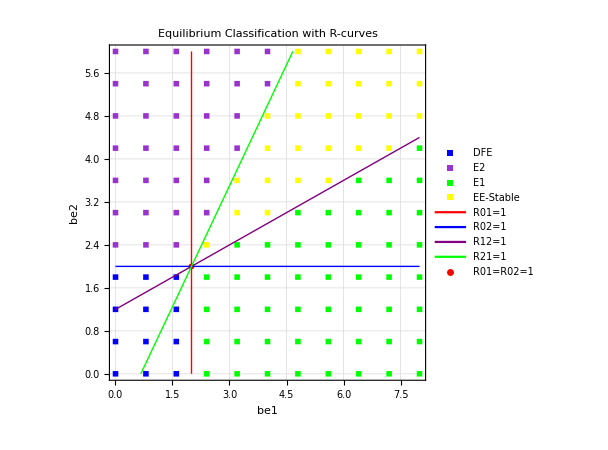

```mathematica
plotInd={3,4};
steTol=10^(-8);
staTol=10^(-10);
choTol=10^(-13);
Timing[{fPl,unC,res}=scan[RHS,var,par,coP,plotInd,mSi,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]fPl
```

```mathematica
Export["RahmanScan.pdf",fPl]
```

RahmanScan.pdf

```mathematica
scanPar[RHS, var, par, p0val, plotInd]
```

Varying parameters at indices {3,4} with center values: {4,3}

Using range mode with step size 1/20...

Total points to scan: 19200

Scanning complete!

```mathematica
Clear[scan4TS]

(*Simplified Time Series Simulation-based multiple equilibrium scanning*)
scan4TS[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,tMax_:100,nInitials_:8,steadyTol_:10^(-6)]:=Block[{bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem,I1Index,I2Index,solTol},(*Define colors*)betterColors={RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0.8,0.5,0.2],RGBColor[0.6,0.3,0.8],RGBColor[1,1,0],RGBColor[1,0.5,0],RGBColor[0,0.8,0.8],RGBColor[0.8,0,0.8],RGBColor[0.5,0.8,0.5],RGBColor[0.8,0.8,0.5],RGBColor[1.0,0.0,1.0]};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
If[useGridMode,(*GRID MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[Randos0^(-1)  *Real[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax}]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify equilibria*)If[Length[uniqueSols]>1,eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
eqTypes=Sort[DeleteDuplicates[eqTypes]];
currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",True,"Multiple"];,(*Single attractor*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No solutions found*)res=Append[res,{N[bifP1],N[bifP2],"NotGAS"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create simple plot*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->outcomes,AspectRatio->1,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add original plot if provided*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot]];
(*Simple summary*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NotGAS points as errors*)unClassifPoints=Select[res,#[[3]]=="NotGAS"&];
{finalPlot,unClassifPoints,res}];
```

DFE: 42 (3%)

NotGAS: 211 (17%)

E2: 341 (28%)

E1: 440 (36%)

EE: 191 (16%)

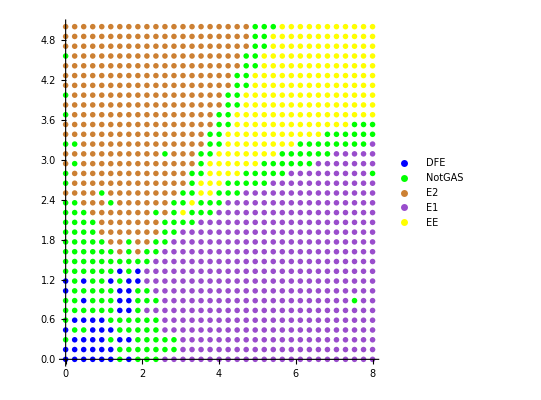

```mathematica
plotInd={1,2};
{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,Automatic,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)];fPl
```

DFE: 48 (4%)

NotGAS: 149 (12%)

E2: 356 (29%)

E1: 453 (37%)

EE: 219 (18%)

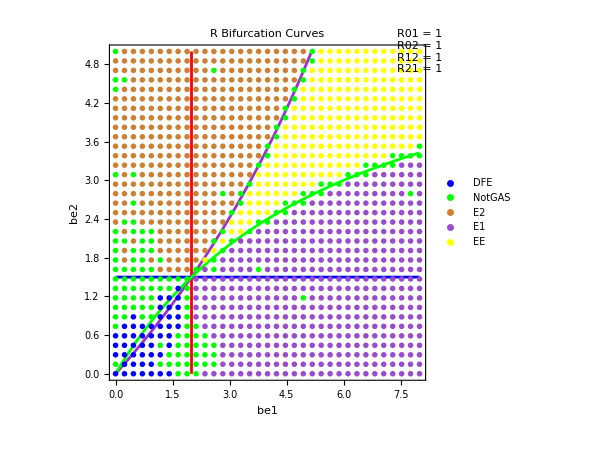

```mathematica
tMax=200;nIc=8;{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,tMax,nIc,10^(-6)];fPl
```

I1 at index 2, I2 at index 5

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 60×60 points...

Total points to scan: 3600

Initial conditions created

Scanning complete!

Found equilibrium types: {DFE (270 points),E2 (919 points),E1 (1291 points),EE (236 points),E1-E2 (344 points),error (18 points),EE-E2 (88 points),EE-E1 (213 points),Coexist (221 points)}

Including 18 errors

Summary:

DFE | 270 | 8%
E2 | 919 | 26%
E1 | 1291 | 36%
EE | 236 | 7%
E1-E2 | 344 | 10%
error | 18 | 0%
EE-E2 | 88 | 2%
EE-E1 | 213 | 6%
Coexist | 221 | 6%

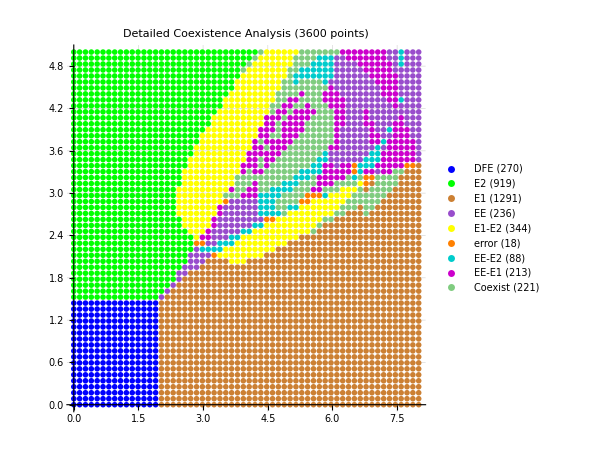

Varying be1 (center=4) and be2 (center=5/2)

Ranges: be1 ∈ {0.,8.}, be2 ∈ {0.,5.}

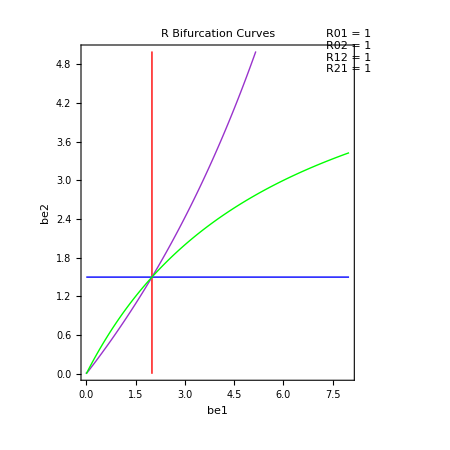

```mathematica
(*Multiple equilibrium scanning with coexistence detection*)scan4[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic]:=Module[{(*Parameter ranges and scanning*)be1,be2,be1min,be1max,be2min,be2max,stepSize,be1vals,be2vals,totalPoints,(*Results collection*)res,outcomes,outcomeCounts,(*Plotting and visualization*)finalPlot,plotData,betterColors,simpleTooltips,(*Mode detection*)useGridMode,be1Index,be2Index,be1Center,be2Center,(*Progress tracking*)progressVar,currentProgress,(*R curve variables*)R01F,R02F,R21F,R12F,rCurves,coPForR,(*Multiple equilibrium variables*)numpar,conPar,inP,in0,in1,in2,sol0,sol1,sol2,solMain,I1val,I2val,tol,currentType,errors,gridResults,nB1,nB2,(*Index finding*)I1Index,I2Index,solTol,allSols,uniqueSols,eqType,eqTypes},(*Define colors including detailed coexistence categories*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EE*)RGBColor[1,1,0],(*Yellow for EE-E1*)RGBColor[1,0.5,0],(*Red-Orange for EE-E2*)RGBColor[0,0.8,0.8],(*Cyan for E1-E2*)RGBColor[0.8,0,0.8],(*Magenta for EE-DFE*)RGBColor[0.5,0.8,0.5],(*Light Green for E1-DFE*)RGBColor[0.8,0.8,0.5],(*Light Orange for E2-DFE*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
Print["I1 at index ",I1Index,", I2 at index ",I2Index];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract parameter indices*)be1Index=If[Length[plotInd]>=1,plotInd[[1]],1];
be2Index=If[Length[plotInd]>=2,plotInd[[2]],2];
be1Center=p0val[[be1Index]];
be2Center=p0val[[be2Index]];
Print["Varying parameters at indices ",{be1Index,be2Index}," with center values: ",{be1Center,be2Center}];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
be1min=Max[be1Center*(1-wRan),0.001];
be1max=be1Center*(1+wRan);
be2min=Max[be2Center*(1-hRan),0.001];
be2max=be2Center*(1+hRan);
be1vals=Table[be1min+(be1max-be1min)*k/(gridRes-1),{k,0,gridRes-1}];
be2vals=Table[be2min+(be2max-be2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
be1min=Max[be1Center*(1-wRan),0.001];
be1max=be1Center*(1+wRan);
be2min=Max[be2Center*(1-hRan),0.001];
be2max=be2Center*(1+hRan);
be1vals=Table[be1,{be1,be1min,be1max,delta}];
be2vals=Table[be2,{be2,be2min,be2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[par[[be1Index]]->_]|HoldPattern[par[[be2Index]]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{par[[be1Index]],be1min,be1max},{par[[be2Index]],be2min,be2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{par[[be1Index]],be1min,be1max},{par[[be2Index]],be2min,be2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{par[[be1Index]],be1min,be1max},{par[[be2Index]],be2min,be2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{par[[be1Index]],be1min,be1max},{par[[be2Index]],be2min,be2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[be1vals]*Length[be2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for multiple equilibrium scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);(*Tolerance for comparing solutions*)(*Create initial condition arrays*)inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];(*General initial*)in0=inP;in0[[I1Index,2]]=0;in0[[I2Index,2]]=0;(*DFE:I1=I2=0*)in1=inP;in1[[I2Index,2]]=0;(*E1:I2=0*)in2=inP;in2[[I1Index,2]]=0;(*E2:I1=0*)Print["Initial conditions created"];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP WITH 4 EQUILIBRIUM SEARCHES*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[be1Index]]=be1;
numpar[[be2Index]]=be2;
conPar=Thread[par->numpar];
(*Four FindRoot calls with different initial conditions*)solMain=Quiet[FindRoot[RHS/. conPar,inP]];(*General*)sol0=Quiet[FindRoot[RHS/. conPar,in0]];(*DFE-like*)sol1=Quiet[FindRoot[RHS/. conPar,in1]];(*E1-like*)sol2=Quiet[FindRoot[RHS/. conPar,in2]];(*E2-like*)(*Collect all successful solutions*)allSols={};
If[Head[solMain]===List,AppendTo[allSols,var/. solMain]];
If[Head[sol0]===List,AppendTo[allSols,var/. sol0]];
If[Head[sol1]===List,AppendTo[allSols,var/. sol1]];
If[Head[sol2]===List,AppendTo[allSols,var/. sol2]];
If[Length[allSols]>0,(*Find unique solutions (within tolerance)*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify based on number of unique equilibria*)If[Length[uniqueSols]>1,(*Multiple equilibria-classify each and determine coexistence type*)eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
(*Remove duplicates and sort to get consistent naming*)eqTypes=Sort[DeleteDuplicates[eqTypes]];
(*Determine coexistence type*)currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",ContainsAll[eqTypes,{"EE","DFE"}]&&Length[eqTypes]==2,"EE-DFE",ContainsAll[eqTypes,{"E1","DFE"}]&&Length[eqTypes]==2,"E1-DFE",ContainsAll[eqTypes,{"E2","DFE"}]&&Length[eqTypes]==2,"E2-DFE",True,"Coexist" (*For 3+types or unexpected combinations*)];,(*Single equilibrium-classify by I1,I2 values*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[be1],N[be2],currentType}];,(*All FindRoot calls failed*)res=Append[res,{N[be1],N[be2],"NoSol"}];];,{be2,be2vals}];,{be1,be1vals}];
Print["Scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{be1vals[[i]],be2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{be1vals[[i]],be2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{be1vals[[i]],be2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": be1="<>ToString[Round[res[[j,1]],0.01]]<>", be2="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Detailed Coexistence Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{"Parameter "<>ToString[be1Index],"Parameter "<>ToString[be2Index]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{be1min,be1max},{be2min,be2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{be1min,be2min},{be1max,be2max}],Blue,PointSize[0.015],Point[{{be1Center,be2Center}}]}],PlotRange->{{be1min*0.9,be1max*1.1},{be2min*0.9,be2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Grid mode:scan4[RHS,var,par,p0val,{1,2},8,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12]*)
(*Range mode:scan4[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05,1.0,1.0,R01,R02,R21,R12]*)
(*Colors:DFE=Blue,E1=Green,E2=Orange,EE=Purple*)
(*Coexistence:EE-E1=Yellow,EE-E2=Red-Orange,E1-E2=Cyan,EE-DFE=Magenta,E1-DFE=Light Green,E2-DFE=Light Orange*)
{fPl,errors,res}=scan4[RHS,var,par,p0val,{1,2},60];fPl
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 30×30 points...

Total points to scan: 900

Scanning complete!

Found equilibrium types: {DFE (72 points),E2 (294 points),E1 (352 points),EEstable (182 points)}

Including 0 errors

Summary:

DFE | 72 | 8%
E2 | 294 | 33%
E1 | 352 | 39%
EEstable | 182 | 20%

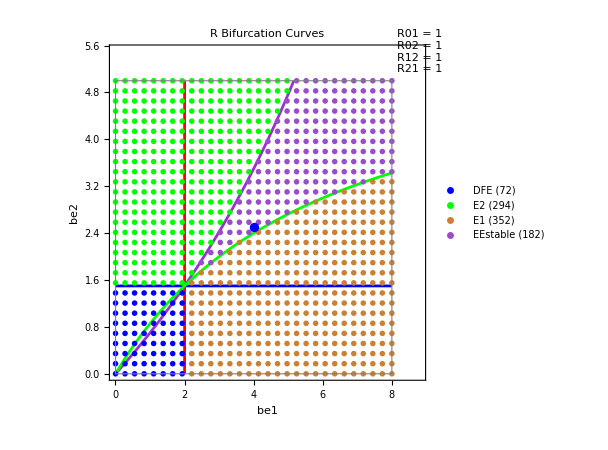

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,plotInd,30,plot];plF
```

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05];plot
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using range mode with step size 0.05...

Total points to scan: 16000

Scanning complete!

Found equilibrium types: {DFE (1200 points),E2 (5206 points),E1 (6379 points),EEstable (3215 points)}

Including 0 errors

Summary:

DFE | 1200 | 8%
E2 | 5206 | 33%
E1 | 6379 | 40%
EEstable | 3215 | 20%

-Graphics-

```mathematica
Evaluate[EpidCRN`invN][1,2,3,4,5,6]
```

R0A has 0 elements

Invasion numbers: R12 = nonRat, R21 = nonRat

At least one equilibrium irrational - coexistence analysis not possible

{nonRat,nonRat,unknown}

```mathematica
(*From LogicalExpand result*)cases=LogicalExpand[expr]//List@@#&;

(*Make disjoint manually*)
disjointCases={cases[[1]],cases[[2]]&&!cases[[1]],cases[[3]]&&!cases[[2]]&&!cases[[1]],(*etc.*)}
```

(R_1>R_3&&R_3>1&&μ_0<(μ_1 μ_3 (R_1-R_3))/(eta (-1+R_1) s_0)&&R_2<R_1)||(R_1>1&&R_1>R_2&&μ_1 μ_3 (-R_1+R_3)+eta μ_0 (-1+R_1) s_0<0&&R_3≤1)

```mathematica
?EpidCRN`*
```